```mathematica
expectedX[0] := 1;
expectedX[2] := x2;
expectedX[4] := 1/(3g)(E0 - 2 x2);
expectedX[u_?EvenQ] := (4 (-3+u) E0 expectedX[(-3+u)-1]+(-3+u) ((-3+u)-1) ((-3+u)-2) expectedX[(-3+u)-3]-4 ((-3+u)+1) expectedX[(-3+u)+1])/(4 g ((-3+u)+2));
expectedX[_?OddQ] := 0;
```

```mathematica
matPositive[K_] := Table[expectedX[i + j], {i, 0, K}, {j, 0, K}];
```

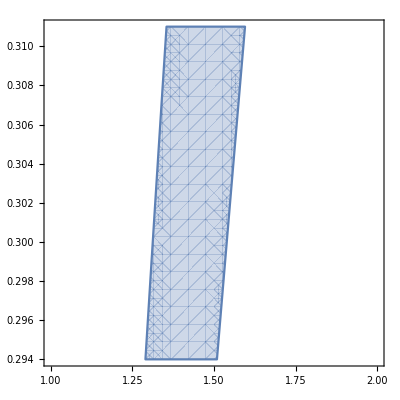

```mathematica
region = Reduce[Det[FullSimplify[matPositive[4] /. g -> 1]] ≥ 0, {E0, x2}];
RegionPlot[region, {E0, 1, 2}, {x2, 0.294, 0.311}]
```

```mathematica
Eigenvalues[matPositive[6]]
```

{1/(6930 g^5)Root[-300529152 E0^3 g^9-676190592 E0^2 g^10-1408730400 E0^4 g^10-6846429744 E0 g^11+64684204200 E0^3 g^11+8985939039 g^12+1159183872 E0^2 g^9 x2+4153742208 E0 g^10 x2+6134014656 E0^3 g^10 x2+12877808328 g^11 x2-179216669016 E0^2 g^11 x2+4427438400 E0^4 g^11 x2-306155856006 E0 g^12 x2-1030385664 E0 g^9 x2^2-5602722048 g^10 x2^2-4733334144 E0^2 g^10 x2^2+83187542592 E0 g^11 x2^2-1505329056 E0^3 g^11 x2^2+496954804500 g^12 x2^2-319300819992 E0^2 g^12 x2^2-171730944 g^9 x2^3-3799547136 E0 g^10 x2^3+26497548000 g^11 x2^3-17959300128 E0^2 g^11 x2^3+314700309000 E0 g^12 x2^3-21300003648 E0^3 g^12 x2^3+1528220925000 g^13 x2^3+(92928 E0^2 g^4-209088 E0 g^5+139392 E0^3 g^5+117612 g^6-31461936 E0^2 g^6-2722500 E0^4 g^6+39060252 E0 g^7-4322241 g^8-5336100 E0^2 g^8-371712 E0 g^4 x2+418176 g^5 x2-975744 E0^2 g^5 x2+87619488 E0 g^6 x2+4599936 E0^3 g^6 x2-34937298 g^7 x2+15714270 E0^2 g^7 x2+95836356 E0 g^8 x2+14407470 g^9 x2+371712 g^4 x2^2+1393920 E0 g^5 x2^2-48450336 g^6 x2^2+2160576 E0^2 g^6 x2^2+68384844 E0 g^7 x2^2+13446972 E0^3 g^7 x2^2-494493120 g^8 x2^2+5122656 E0^2 g^8 x2^2+28814940 E0 g^9 x2^2) #1+(1408 E0 g-1584 g^2+2904 E0^2 g^2-13244 E0 g^3-2079 g^4-2816 g x2-8976 E0 g^2 x2+36454 g^3 x2-3234 E0^2 g^3 x2-4158 E0 g^4 x2-6930 g^5 x2) #1^2+#1^3&,1],1/(6930 g^5)Root[-300529152 E0^3 g^9-676190592 E0^2 g^10-1408730400 E0^4 g^10-6846429744 E0 g^11+64684204200 E0^3 g^11+8985939039 g^12+1159183872 E0^2 g^9 x2+4153742208 E0 g^10 x2+6134014656 E0^3 g^10 x2+12877808328 g^11 x2-179216669016 E0^2 g^11 x2+4427438400 E0^4 g^11 x2-306155856006 E0 g^12 x2-1030385664 E0 g^9 x2^2-5602722048 g^10 x2^2-4733334144 E0^2 g^10 x2^2+83187542592 E0 g^11 x2^2-1505329056 E0^3 g^11 x2^2+496954804500 g^12 x2^2-319300819992 E0^2 g^12 x2^2-171730944 g^9 x2^3-3799547136 E0 g^10 x2^3+26497548000 g^11 x2^3-17959300128 E0^2 g^11 x2^3+314700309000 E0 g^12 x2^3-21300003648 E0^3 g^12 x2^3+1528220925000 g^13 x2^3+(92928 E0^2 g^4-209088 E0 g^5+139392 E0^3 g^5+117612 g^6-31461936 E0^2 g^6-2722500 E0^4 g^6+39060252 E0 g^7-4322241 g^8-5336100 E0^2 g^8-371712 E0 g^4 x2+418176 g^5 x2-975744 E0^2 g^5 x2+87619488 E0 g^6 x2+4599936 E0^3 g^6 x2-34937298 g^7 x2+15714270 E0^2 g^7 x2+95836356 E0 g^8 x2+14407470 g^9 x2+371712 g^4 x2^2+1393920 E0 g^5 x2^2-48450336 g^6 x2^2+2160576 E0^2 g^6 x2^2+68384844 E0 g^7 x2^2+13446972 E0^3 g^7 x2^2-494493120 g^8 x2^2+5122656 E0^2 g^8 x2^2+28814940 E0 g^9 x2^2) #1+(1408 E0 g-1584 g^2+2904 E0^2 g^2-13244 E0 g^3-2079 g^4-2816 g x2-8976 E0 g^2 x2+36454 g^3 x2-3234 E0^2 g^3 x2-4158 E0 g^4 x2-6930 g^5 x2) #1^2+#1^3&,2],1/(6930 g^5)Root[-300529152 E0^3 g^9-676190592 E0^2 g^10-1408730400 E0^4 g^10-6846429744 E0 g^11+64684204200 E0^3 g^11+8985939039 g^12+1159183872 E0^2 g^9 x2+4153742208 E0 g^10 x2+6134014656 E0^3 g^10 x2+12877808328 g^11 x2-179216669016 E0^2 g^11 x2+4427438400 E0^4 g^11 x2-306155856006 E0 g^12 x2-1030385664 E0 g^9 x2^2-5602722048 g^10 x2^2-4733334144 E0^2 g^10 x2^2+83187542592 E0 g^11 x2^2-1505329056 E0^3 g^11 x2^2+496954804500 g^12 x2^2-319300819992 E0^2 g^12 x2^2-171730944 g^9 x2^3-3799547136 E0 g^10 x2^3+26497548000 g^11 x2^3-17959300128 E0^2 g^11 x2^3+314700309000 E0 g^12 x2^3-21300003648 E0^3 g^12 x2^3+1528220925000 g^13 x2^3+(92928 E0^2 g^4-209088 E0 g^5+139392 E0^3 g^5+117612 g^6-31461936 E0^2 g^6-2722500 E0^4 g^6+39060252 E0 g^7-4322241 g^8-5336100 E0^2 g^8-371712 E0 g^4 x2+418176 g^5 x2-975744 E0^2 g^5 x2+87619488 E0 g^6 x2+4599936 E0^3 g^6 x2-34937298 g^7 x2+15714270 E0^2 g^7 x2+95836356 E0 g^8 x2+14407470 g^9 x2+371712 g^4 x2^2+1393920 E0 g^5 x2^2-48450336 g^6 x2^2+2160576 E0^2 g^6 x2^2+68384844 E0 g^7 x2^2+13446972 E0^3 g^7 x2^2-494493120 g^8 x2^2+5122656 E0^2 g^8 x2^2+28814940 E0 g^9 x2^2) #1+(1408 E0 g-1584 g^2+2904 E0^2 g^2-13244 E0 g^3-2079 g^4-2816 g x2-8976 E0 g^2 x2+36454 g^3 x2-3234 E0^2 g^3 x2-4158 E0 g^4 x2-6930 g^5 x2) #1^2+#1^3&,3],1/(6930 g^5)Root[10303856640 E0^3 g^11+776653194240 E0^2 g^12+362180560896 E0^4 g^12-1786592142720 E0 g^13+7002082378368 E0^3 g^13+1917483321600 E0^5 g^13+1012293540720 g^14-250112068856496 E0^2 g^14-56065054953600 E0^4 g^14+2414966400000 E0^6 g^14+889440227332272 E0 g^15-2348172554943600 E0^3 g^15-694622073653739 g^16-61823139840 E0^2 g^11 x2-3106612776960 E0 g^12 x2-1676437475328 E0^3 g^12 x2+3573184285440 g^13 x2-14338911299328 E0^2 g^13 x2-8858483149824 E0^4 g^13 x2+948456705297024 E0 g^14 x2+305610069574656 E0^3 g^14 x2-12287349043200 E0^5 g^14 x2-1757152820841264 g^15 x2+9828726281301312 E0^2 g^15 x2+363268905753600 E0^4 g^15 x2+7860947396325408 E0 g^16 x2+123646279680 E0 g^11 x2^2+3106612776960 g^12 x2^2+2309094273024 E0^2 g^12 x2^2-36093508222464 E0 g^13 x2^2+9540469661184 E0^3 g^13 x2^2-887056184577024 g^14 x2^2-652995709115904 E0^2 g^14 x2^2+4628621200896 E0^4 g^14 x2^2-8799507762512544 E0 g^15 x2^2-832852939919616 E0^3 g^15 x2^2-17040002918400 E0^5 g^15 x2^2-19695099993030000 g^16 x2^2+17403262912927584 E0^2 g^16 x2^2-82430853120 g^11 x2^3-708905336832 E0 g^12 x2^3+73526002615296 g^13 x2^3+2224860244992 E0^2 g^13 x2^3+470665101924864 E0 g^14 x2^3+26871427731456 E0^3 g^14 x2^3-2696348222568000 g^15 x2^3-206143270679808 E0^2 g^15 x2^3+47257608093696 E0^4 g^15 x2^3-37585148443920000 E0 g^16 x2^3-1734445097054208 E0^3 g^16 x2^3-33323162913810000 g^17 x2^3-201955590144 g^12 x2^4-2423467081728 E0 g^13 x2^4+149494470048000 g^14 x2^4-7355601259776 E0^2 g^14 x2^4+1161441865584000 E0 g^15 x2^4+3038800520448 E0^3 g^15 x2^4-981057459690000 g^16 x2^4+1925875329840000 E0^2 g^16 x2^4+26241604494336 E0^4 g^16 x2^4-29923176999870000 E0 g^17 x2^4+(-1486848 E0^3 g^6-424309248 E0^2 g^7-116531712 E0^4 g^7+960341184 E0 g^8-2080402368 E0^3 g^8-623082240 E0^5 g^8-541250424 g^9+139625220240 E0^2 g^9+29102131080 E0^4 g^9-653400000 E0^6 g^9-519896573658 E0 g^10+93721710390 E0^3 g^10-8232840000 E0^5 g^10+411319272672 g^11+1817026131690 E0^2 g^11-2744280000 E0^4 g^11-395960498010 E0 g^12-14087304000 E0^3 g^12+29953130130 g^13+8921088 E0^2 g^6 x2+1697236992 E0 g^7 x2+475047936 E0^3 g^7 x2-1920682368 g^8 x2+7798285440 E0^2 g^8 x2+2709501696 E0^4 g^8 x2-554114528352 E0 g^9 x2-110891075328 E0^3 g^9 x2+3679426080 E0^5 g^9 x2+1041437833524 g^10 x2-1405985897844 E0^2 g^10 x2-117854062920 E0^4 g^10 x2-5816694672558 E0 g^11 x2-89480908440 E0^3 g^11 x2-1910029171050 g^12 x2-583529977800 E0^2 g^12 x2-184473245880 E0 g^13 x2-17842176 E0 g^6 x2^2-1697236992 g^7 x2^2-501811200 E0^2 g^7 x2^2-1355726592 E0 g^8 x2^2-2329797888 E0^3 g^8 x2^2+544813875936 g^9 x2^2+121703643072 E0^2 g^9 x2^2-1574328096 E0^4 g^9 x2^2+2046165947496 E0 g^10 x2^2+119339110440 E0^3 g^10 x2^2+3124820160 E0^5 g^10 x2^2+7865174912760 g^11 x2^2+138707776944 E0^2 g^11 x2^2+38880959040 E0^4 g^11 x2^2-6557898889080 E0 g^12 x2^2+9681819840 E0^3 g^12 x2^2+2766975195600 g^13 x2^2+65928582720 E0^2 g^13 x2^2+11894784 g^6 x2^3+35684352 E0 g^7 x2^3-11838469632 g^8 x2^3-1193753088 E0^2 g^8 x2^3-39327222528 E0 g^9 x2^3-7510440960 E0^3 g^9 x2^3+763256258160 g^10 x2^3+268046094096 E0^2 g^10 x2^3-11643797088 E0^4 g^10 x2^3+4584039039360 E0 g^11 x2^3+639703193976 E0^3 g^11 x2^3+6286048421400 g^12 x2^3+161536553640 E0^2 g^12 x2^3+1951635886200 E0 g^13 x2^3+713169765000 g^14 x2^3) #1+(45056 E0^2 g^2-101376 E0 g^3+168960 E0^3 g^3+57024 g^4-14815328 E0^2 g^4+199584 E0^4 g^4+65867868 E0 g^5+29142696 E0^3 g^5+2227500 E0^5 g^5-55591272 g^6-242448712 E0^2 g^6+396000 E0^4 g^6-174638772 E0 g^7+13167000 E0^3 g^7+144037278 g^8+6098400 E0^2 g^8+16008300 E0 g^9-180224 E0 g^2 x2+202752 g^3 x2-878592 E0^2 g^3 x2+59785088 E0 g^4 x2-1347456 E0^3 g^4 x2-132496056 g^5 x2+22753104 E0^2 g^5 x2-4600728 E0^4 g^5 x2+618860704 E0 g^6 x2+17715984 E0^3 g^6 x2+798418764 g^7 x2+37046196 E0^2 g^7 x2+387763992 E0 g^8 x2+70893900 g^9 x2+180224 g^2 x2^2+1081344 E0 g^3 x2^2-59852672 g^4 x2^2+2124672 E0^2 g^4 x2^2-163217472 E0 g^5 x2^2+671616 E0^3 g^5 x2^2-724125292 g^6 x2^2-285268368 E0^2 g^6 x2^2-10458756 E0^4 g^6 x2^2+785629548 E0 g^7 x2^2-310473900 g^8 x2^2-34577928 E0^2 g^8 x2^2-48024900 g^10 x2^2) #1^2+(-1280 E0+1440 g-3936 E0^2 g+34762 E0 g^2-1350 E0^3 g^2-22032 g^3-1650 E0^2 g^3-2310 E0 g^4-6930 g^5+2560 x2+10752 E0 g x2-75668 g^2 x2+8556 E0^2 g^2 x2-52914 E0 g^3 x2-10230 g^4 x2) #1^3+#1^4&,1],1/(6930 g^5)Root[10303856640 E0^3 g^11+776653194240 E0^2 g^12+362180560896 E0^4 g^12-1786592142720 E0 g^13+7002082378368 E0^3 g^13+1917483321600 E0^5 g^13+1012293540720 g^14-250112068856496 E0^2 g^14-56065054953600 E0^4 g^14+2414966400000 E0^6 g^14+889440227332272 E0 g^15-2348172554943600 E0^3 g^15-694622073653739 g^16-61823139840 E0^2 g^11 x2-3106612776960 E0 g^12 x2-1676437475328 E0^3 g^12 x2+3573184285440 g^13 x2-14338911299328 E0^2 g^13 x2-8858483149824 E0^4 g^13 x2+948456705297024 E0 g^14 x2+305610069574656 E0^3 g^14 x2-12287349043200 E0^5 g^14 x2-1757152820841264 g^15 x2+9828726281301312 E0^2 g^15 x2+363268905753600 E0^4 g^15 x2+7860947396325408 E0 g^16 x2+123646279680 E0 g^11 x2^2+3106612776960 g^12 x2^2+2309094273024 E0^2 g^12 x2^2-36093508222464 E0 g^13 x2^2+9540469661184 E0^3 g^13 x2^2-887056184577024 g^14 x2^2-652995709115904 E0^2 g^14 x2^2+4628621200896 E0^4 g^14 x2^2-8799507762512544 E0 g^15 x2^2-832852939919616 E0^3 g^15 x2^2-17040002918400 E0^5 g^15 x2^2-19695099993030000 g^16 x2^2+17403262912927584 E0^2 g^16 x2^2-82430853120 g^11 x2^3-708905336832 E0 g^12 x2^3+73526002615296 g^13 x2^3+2224860244992 E0^2 g^13 x2^3+470665101924864 E0 g^14 x2^3+26871427731456 E0^3 g^14 x2^3-2696348222568000 g^15 x2^3-206143270679808 E0^2 g^15 x2^3+47257608093696 E0^4 g^15 x2^3-37585148443920000 E0 g^16 x2^3-1734445097054208 E0^3 g^16 x2^3-33323162913810000 g^17 x2^3-201955590144 g^12 x2^4-2423467081728 E0 g^13 x2^4+149494470048000 g^14 x2^4-7355601259776 E0^2 g^14 x2^4+1161441865584000 E0 g^15 x2^4+3038800520448 E0^3 g^15 x2^4-981057459690000 g^16 x2^4+1925875329840000 E0^2 g^16 x2^4+26241604494336 E0^4 g^16 x2^4-29923176999870000 E0 g^17 x2^4+(-1486848 E0^3 g^6-424309248 E0^2 g^7-116531712 E0^4 g^7+960341184 E0 g^8-2080402368 E0^3 g^8-623082240 E0^5 g^8-541250424 g^9+139625220240 E0^2 g^9+29102131080 E0^4 g^9-653400000 E0^6 g^9-519896573658 E0 g^10+93721710390 E0^3 g^10-8232840000 E0^5 g^10+411319272672 g^11+1817026131690 E0^2 g^11-2744280000 E0^4 g^11-395960498010 E0 g^12-14087304000 E0^3 g^12+29953130130 g^13+8921088 E0^2 g^6 x2+1697236992 E0 g^7 x2+475047936 E0^3 g^7 x2-1920682368 g^8 x2+7798285440 E0^2 g^8 x2+2709501696 E0^4 g^8 x2-554114528352 E0 g^9 x2-110891075328 E0^3 g^9 x2+3679426080 E0^5 g^9 x2+1041437833524 g^10 x2-1405985897844 E0^2 g^10 x2-117854062920 E0^4 g^10 x2-5816694672558 E0 g^11 x2-89480908440 E0^3 g^11 x2-1910029171050 g^12 x2-583529977800 E0^2 g^12 x2-184473245880 E0 g^13 x2-17842176 E0 g^6 x2^2-1697236992 g^7 x2^2-501811200 E0^2 g^7 x2^2-1355726592 E0 g^8 x2^2-2329797888 E0^3 g^8 x2^2+544813875936 g^9 x2^2+121703643072 E0^2 g^9 x2^2-1574328096 E0^4 g^9 x2^2+2046165947496 E0 g^10 x2^2+119339110440 E0^3 g^10 x2^2+3124820160 E0^5 g^10 x2^2+7865174912760 g^11 x2^2+138707776944 E0^2 g^11 x2^2+38880959040 E0^4 g^11 x2^2-6557898889080 E0 g^12 x2^2+9681819840 E0^3 g^12 x2^2+2766975195600 g^13 x2^2+65928582720 E0^2 g^13 x2^2+11894784 g^6 x2^3+35684352 E0 g^7 x2^3-11838469632 g^8 x2^3-1193753088 E0^2 g^8 x2^3-39327222528 E0 g^9 x2^3-7510440960 E0^3 g^9 x2^3+763256258160 g^10 x2^3+268046094096 E0^2 g^10 x2^3-11643797088 E0^4 g^10 x2^3+4584039039360 E0 g^11 x2^3+639703193976 E0^3 g^11 x2^3+6286048421400 g^12 x2^3+161536553640 E0^2 g^12 x2^3+1951635886200 E0 g^13 x2^3+713169765000 g^14 x2^3) #1+(45056 E0^2 g^2-101376 E0 g^3+168960 E0^3 g^3+57024 g^4-14815328 E0^2 g^4+199584 E0^4 g^4+65867868 E0 g^5+29142696 E0^3 g^5+2227500 E0^5 g^5-55591272 g^6-242448712 E0^2 g^6+396000 E0^4 g^6-174638772 E0 g^7+13167000 E0^3 g^7+144037278 g^8+6098400 E0^2 g^8+16008300 E0 g^9-180224 E0 g^2 x2+202752 g^3 x2-878592 E0^2 g^3 x2+59785088 E0 g^4 x2-1347456 E0^3 g^4 x2-132496056 g^5 x2+22753104 E0^2 g^5 x2-4600728 E0^4 g^5 x2+618860704 E0 g^6 x2+17715984 E0^3 g^6 x2+798418764 g^7 x2+37046196 E0^2 g^7 x2+387763992 E0 g^8 x2+70893900 g^9 x2+180224 g^2 x2^2+1081344 E0 g^3 x2^2-59852672 g^4 x2^2+2124672 E0^2 g^4 x2^2-163217472 E0 g^5 x2^2+671616 E0^3 g^5 x2^2-724125292 g^6 x2^2-285268368 E0^2 g^6 x2^2-10458756 E0^4 g^6 x2^2+785629548 E0 g^7 x2^2-310473900 g^8 x2^2-34577928 E0^2 g^8 x2^2-48024900 g^10 x2^2) #1^2+(-1280 E0+1440 g-3936 E0^2 g+34762 E0 g^2-1350 E0^3 g^2-22032 g^3-1650 E0^2 g^3-2310 E0 g^4-6930 g^5+2560 x2+10752 E0 g x2-75668 g^2 x2+8556 E0^2 g^2 x2-52914 E0 g^3 x2-10230 g^4 x2) #1^3+#1^4&,2],1/(6930 g^5)Root[10303856640 E0^3 g^11+776653194240 E0^2 g^12+362180560896 E0^4 g^12-1786592142720 E0 g^13+7002082378368 E0^3 g^13+1917483321600 E0^5 g^13+1012293540720 g^14-250112068856496 E0^2 g^14-56065054953600 E0^4 g^14+2414966400000 E0^6 g^14+889440227332272 E0 g^15-2348172554943600 E0^3 g^15-694622073653739 g^16-61823139840 E0^2 g^11 x2-3106612776960 E0 g^12 x2-1676437475328 E0^3 g^12 x2+3573184285440 g^13 x2-14338911299328 E0^2 g^13 x2-8858483149824 E0^4 g^13 x2+948456705297024 E0 g^14 x2+305610069574656 E0^3 g^14 x2-12287349043200 E0^5 g^14 x2-1757152820841264 g^15 x2+9828726281301312 E0^2 g^15 x2+363268905753600 E0^4 g^15 x2+7860947396325408 E0 g^16 x2+123646279680 E0 g^11 x2^2+3106612776960 g^12 x2^2+2309094273024 E0^2 g^12 x2^2-36093508222464 E0 g^13 x2^2+9540469661184 E0^3 g^13 x2^2-887056184577024 g^14 x2^2-652995709115904 E0^2 g^14 x2^2+4628621200896 E0^4 g^14 x2^2-8799507762512544 E0 g^15 x2^2-832852939919616 E0^3 g^15 x2^2-17040002918400 E0^5 g^15 x2^2-19695099993030000 g^16 x2^2+17403262912927584 E0^2 g^16 x2^2-82430853120 g^11 x2^3-708905336832 E0 g^12 x2^3+73526002615296 g^13 x2^3+2224860244992 E0^2 g^13 x2^3+470665101924864 E0 g^14 x2^3+26871427731456 E0^3 g^14 x2^3-2696348222568000 g^15 x2^3-206143270679808 E0^2 g^15 x2^3+47257608093696 E0^4 g^15 x2^3-37585148443920000 E0 g^16 x2^3-1734445097054208 E0^3 g^16 x2^3-33323162913810000 g^17 x2^3-201955590144 g^12 x2^4-2423467081728 E0 g^13 x2^4+149494470048000 g^14 x2^4-7355601259776 E0^2 g^14 x2^4+1161441865584000 E0 g^15 x2^4+3038800520448 E0^3 g^15 x2^4-981057459690000 g^16 x2^4+1925875329840000 E0^2 g^16 x2^4+26241604494336 E0^4 g^16 x2^4-29923176999870000 E0 g^17 x2^4+(-1486848 E0^3 g^6-424309248 E0^2 g^7-116531712 E0^4 g^7+960341184 E0 g^8-2080402368 E0^3 g^8-623082240 E0^5 g^8-541250424 g^9+139625220240 E0^2 g^9+29102131080 E0^4 g^9-653400000 E0^6 g^9-519896573658 E0 g^10+93721710390 E0^3 g^10-8232840000 E0^5 g^10+411319272672 g^11+1817026131690 E0^2 g^11-2744280000 E0^4 g^11-395960498010 E0 g^12-14087304000 E0^3 g^12+29953130130 g^13+8921088 E0^2 g^6 x2+1697236992 E0 g^7 x2+475047936 E0^3 g^7 x2-1920682368 g^8 x2+7798285440 E0^2 g^8 x2+2709501696 E0^4 g^8 x2-554114528352 E0 g^9 x2-110891075328 E0^3 g^9 x2+3679426080 E0^5 g^9 x2+1041437833524 g^10 x2-1405985897844 E0^2 g^10 x2-117854062920 E0^4 g^10 x2-5816694672558 E0 g^11 x2-89480908440 E0^3 g^11 x2-1910029171050 g^12 x2-583529977800 E0^2 g^12 x2-184473245880 E0 g^13 x2-17842176 E0 g^6 x2^2-1697236992 g^7 x2^2-501811200 E0^2 g^7 x2^2-1355726592 E0 g^8 x2^2-2329797888 E0^3 g^8 x2^2+544813875936 g^9 x2^2+121703643072 E0^2 g^9 x2^2-1574328096 E0^4 g^9 x2^2+2046165947496 E0 g^10 x2^2+119339110440 E0^3 g^10 x2^2+3124820160 E0^5 g^10 x2^2+7865174912760 g^11 x2^2+138707776944 E0^2 g^11 x2^2+38880959040 E0^4 g^11 x2^2-6557898889080 E0 g^12 x2^2+9681819840 E0^3 g^12 x2^2+2766975195600 g^13 x2^2+65928582720 E0^2 g^13 x2^2+11894784 g^6 x2^3+35684352 E0 g^7 x2^3-11838469632 g^8 x2^3-1193753088 E0^2 g^8 x2^3-39327222528 E0 g^9 x2^3-7510440960 E0^3 g^9 x2^3+763256258160 g^10 x2^3+268046094096 E0^2 g^10 x2^3-11643797088 E0^4 g^10 x2^3+4584039039360 E0 g^11 x2^3+639703193976 E0^3 g^11 x2^3+6286048421400 g^12 x2^3+161536553640 E0^2 g^12 x2^3+1951635886200 E0 g^13 x2^3+713169765000 g^14 x2^3) #1+(45056 E0^2 g^2-101376 E0 g^3+168960 E0^3 g^3+57024 g^4-14815328 E0^2 g^4+199584 E0^4 g^4+65867868 E0 g^5+29142696 E0^3 g^5+2227500 E0^5 g^5-55591272 g^6-242448712 E0^2 g^6+396000 E0^4 g^6-174638772 E0 g^7+13167000 E0^3 g^7+144037278 g^8+6098400 E0^2 g^8+16008300 E0 g^9-180224 E0 g^2 x2+202752 g^3 x2-878592 E0^2 g^3 x2+59785088 E0 g^4 x2-1347456 E0^3 g^4 x2-132496056 g^5 x2+22753104 E0^2 g^5 x2-4600728 E0^4 g^5 x2+618860704 E0 g^6 x2+17715984 E0^3 g^6 x2+798418764 g^7 x2+37046196 E0^2 g^7 x2+387763992 E0 g^8 x2+70893900 g^9 x2+180224 g^2 x2^2+1081344 E0 g^3 x2^2-59852672 g^4 x2^2+2124672 E0^2 g^4 x2^2-163217472 E0 g^5 x2^2+671616 E0^3 g^5 x2^2-724125292 g^6 x2^2-285268368 E0^2 g^6 x2^2-10458756 E0^4 g^6 x2^2+785629548 E0 g^7 x2^2-310473900 g^8 x2^2-34577928 E0^2 g^8 x2^2-48024900 g^10 x2^2) #1^2+(-1280 E0+1440 g-3936 E0^2 g+34762 E0 g^2-1350 E0^3 g^2-22032 g^3-1650 E0^2 g^3-2310 E0 g^4-6930 g^5+2560 x2+10752 E0 g x2-75668 g^2 x2+8556 E0^2 g^2 x2-52914 E0 g^3 x2-10230 g^4 x2) #1^3+#1^4&,3],1/(6930 g^5)Root[10303856640 E0^3 g^11+776653194240 E0^2 g^12+362180560896 E0^4 g^12-1786592142720 E0 g^13+7002082378368 E0^3 g^13+1917483321600 E0^5 g^13+1012293540720 g^14-250112068856496 E0^2 g^14-56065054953600 E0^4 g^14+2414966400000 E0^6 g^14+889440227332272 E0 g^15-2348172554943600 E0^3 g^15-694622073653739 g^16-61823139840 E0^2 g^11 x2-3106612776960 E0 g^12 x2-1676437475328 E0^3 g^12 x2+3573184285440 g^13 x2-14338911299328 E0^2 g^13 x2-8858483149824 E0^4 g^13 x2+948456705297024 E0 g^14 x2+305610069574656 E0^3 g^14 x2-12287349043200 E0^5 g^14 x2-1757152820841264 g^15 x2+9828726281301312 E0^2 g^15 x2+363268905753600 E0^4 g^15 x2+7860947396325408 E0 g^16 x2+123646279680 E0 g^11 x2^2+3106612776960 g^12 x2^2+2309094273024 E0^2 g^12 x2^2-36093508222464 E0 g^13 x2^2+9540469661184 E0^3 g^13 x2^2-887056184577024 g^14 x2^2-652995709115904 E0^2 g^14 x2^2+4628621200896 E0^4 g^14 x2^2-8799507762512544 E0 g^15 x2^2-832852939919616 E0^3 g^15 x2^2-17040002918400 E0^5 g^15 x2^2-19695099993030000 g^16 x2^2+17403262912927584 E0^2 g^16 x2^2-82430853120 g^11 x2^3-708905336832 E0 g^12 x2^3+73526002615296 g^13 x2^3+2224860244992 E0^2 g^13 x2^3+470665101924864 E0 g^14 x2^3+26871427731456 E0^3 g^14 x2^3-2696348222568000 g^15 x2^3-206143270679808 E0^2 g^15 x2^3+47257608093696 E0^4 g^15 x2^3-37585148443920000 E0 g^16 x2^3-1734445097054208 E0^3 g^16 x2^3-33323162913810000 g^17 x2^3-201955590144 g^12 x2^4-2423467081728 E0 g^13 x2^4+149494470048000 g^14 x2^4-7355601259776 E0^2 g^14 x2^4+1161441865584000 E0 g^15 x2^4+3038800520448 E0^3 g^15 x2^4-981057459690000 g^16 x2^4+1925875329840000 E0^2 g^16 x2^4+26241604494336 E0^4 g^16 x2^4-29923176999870000 E0 g^17 x2^4+(-1486848 E0^3 g^6-424309248 E0^2 g^7-116531712 E0^4 g^7+960341184 E0 g^8-2080402368 E0^3 g^8-623082240 E0^5 g^8-541250424 g^9+139625220240 E0^2 g^9+29102131080 E0^4 g^9-653400000 E0^6 g^9-519896573658 E0 g^10+93721710390 E0^3 g^10-8232840000 E0^5 g^10+411319272672 g^11+1817026131690 E0^2 g^11-2744280000 E0^4 g^11-395960498010 E0 g^12-14087304000 E0^3 g^12+29953130130 g^13+8921088 E0^2 g^6 x2+1697236992 E0 g^7 x2+475047936 E0^3 g^7 x2-1920682368 g^8 x2+7798285440 E0^2 g^8 x2+2709501696 E0^4 g^8 x2-554114528352 E0 g^9 x2-110891075328 E0^3 g^9 x2+3679426080 E0^5 g^9 x2+1041437833524 g^10 x2-1405985897844 E0^2 g^10 x2-117854062920 E0^4 g^10 x2-5816694672558 E0 g^11 x2-89480908440 E0^3 g^11 x2-1910029171050 g^12 x2-583529977800 E0^2 g^12 x2-184473245880 E0 g^13 x2-17842176 E0 g^6 x2^2-1697236992 g^7 x2^2-501811200 E0^2 g^7 x2^2-1355726592 E0 g^8 x2^2-2329797888 E0^3 g^8 x2^2+544813875936 g^9 x2^2+121703643072 E0^2 g^9 x2^2-1574328096 E0^4 g^9 x2^2+2046165947496 E0 g^10 x2^2+119339110440 E0^3 g^10 x2^2+3124820160 E0^5 g^10 x2^2+7865174912760 g^11 x2^2+138707776944 E0^2 g^11 x2^2+38880959040 E0^4 g^11 x2^2-6557898889080 E0 g^12 x2^2+9681819840 E0^3 g^12 x2^2+2766975195600 g^13 x2^2+65928582720 E0^2 g^13 x2^2+11894784 g^6 x2^3+35684352 E0 g^7 x2^3-11838469632 g^8 x2^3-1193753088 E0^2 g^8 x2^3-39327222528 E0 g^9 x2^3-7510440960 E0^3 g^9 x2^3+763256258160 g^10 x2^3+268046094096 E0^2 g^10 x2^3-11643797088 E0^4 g^10 x2^3+4584039039360 E0 g^11 x2^3+639703193976 E0^3 g^11 x2^3+6286048421400 g^12 x2^3+161536553640 E0^2 g^12 x2^3+1951635886200 E0 g^13 x2^3+713169765000 g^14 x2^3) #1+(45056 E0^2 g^2-101376 E0 g^3+168960 E0^3 g^3+57024 g^4-14815328 E0^2 g^4+199584 E0^4 g^4+65867868 E0 g^5+29142696 E0^3 g^5+2227500 E0^5 g^5-55591272 g^6-242448712 E0^2 g^6+396000 E0^4 g^6-174638772 E0 g^7+13167000 E0^3 g^7+144037278 g^8+6098400 E0^2 g^8+16008300 E0 g^9-180224 E0 g^2 x2+202752 g^3 x2-878592 E0^2 g^3 x2+59785088 E0 g^4 x2-1347456 E0^3 g^4 x2-132496056 g^5 x2+22753104 E0^2 g^5 x2-4600728 E0^4 g^5 x2+618860704 E0 g^6 x2+17715984 E0^3 g^6 x2+798418764 g^7 x2+37046196 E0^2 g^7 x2+387763992 E0 g^8 x2+70893900 g^9 x2+180224 g^2 x2^2+1081344 E0 g^3 x2^2-59852672 g^4 x2^2+2124672 E0^2 g^4 x2^2-163217472 E0 g^5 x2^2+671616 E0^3 g^5 x2^2-724125292 g^6 x2^2-285268368 E0^2 g^6 x2^2-10458756 E0^4 g^6 x2^2+785629548 E0 g^7 x2^2-310473900 g^8 x2^2-34577928 E0^2 g^8 x2^2-48024900 g^10 x2^2) #1^2+(-1280 E0+1440 g-3936 E0^2 g+34762 E0 g^2-1350 E0^3 g^2-22032 g^3-1650 E0^2 g^3-2310 E0 g^4-6930 g^5+2560 x2+10752 E0 g x2-75668 g^2 x2+8556 E0^2 g^2 x2-52914 E0 g^3 x2-10230 g^4 x2) #1^3+#1^4&,4]}

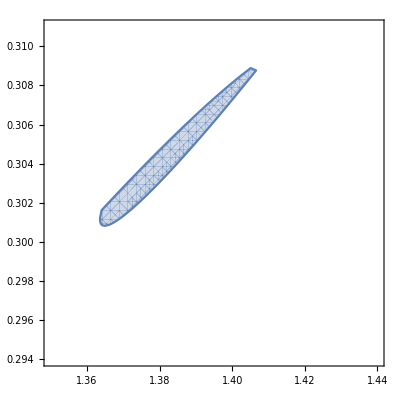

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[8] /. g -> 1], # ≥ 0 &], {E0, 1.35, 1.44}, {x2, 0.294, 0.311}]
```

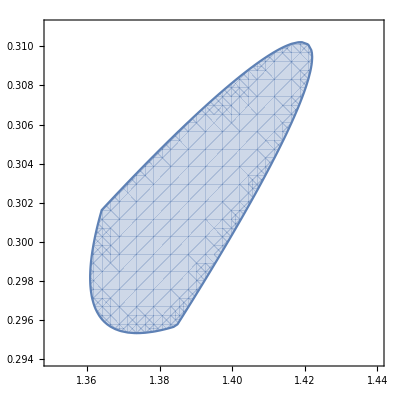

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[7] /. g -> 1], # ≥ 0 &], {E0, 1.35, 1.44}, {x2, 0.294, 0.311}]
```

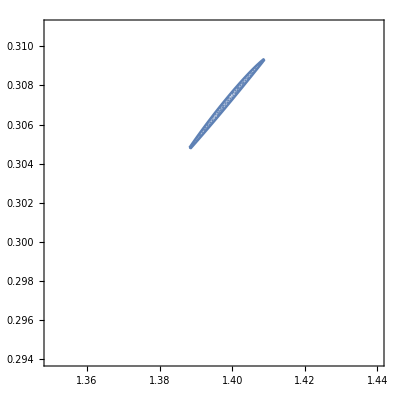

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[9] /. g -> 1], # ≥ 0 &], {E0, 1.35, 1.44}, {x2, 0.294, 0.311}, PlotPoints->100]
```

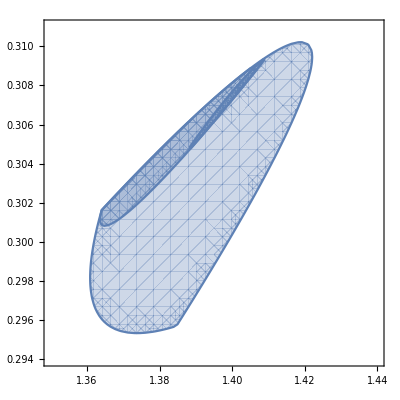

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

上图复现了图1第一张图。

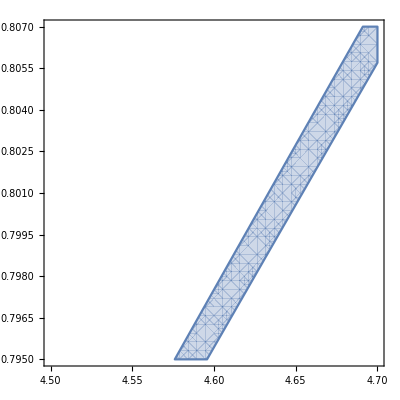

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[7] /. g -> 1], # ≥ 0 &], {E0, 4.50, 4.70}, {x2, 0.795, 0.807}]
```

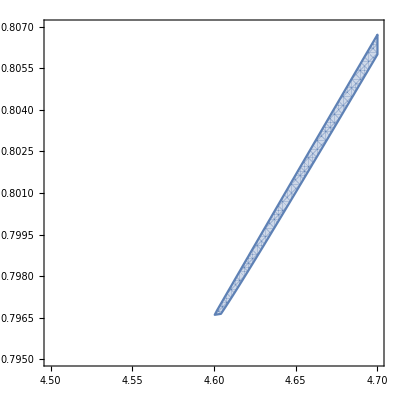

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[9] /. g -> 1], # ≥ 0 &], {E0, 4.50, 4.70}, {x2, 0.795, 0.807}]
```

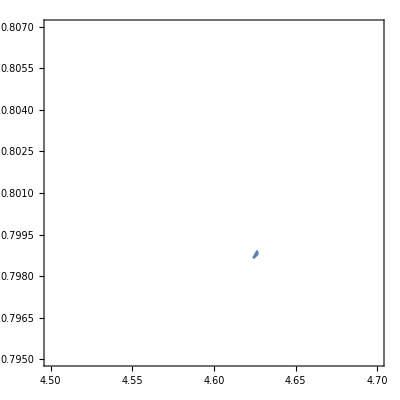

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[11] /. g -> 1], # ≥ 0 &], {E0, 4.50, 4.70}, {x2, 0.795, 0.807}]
```

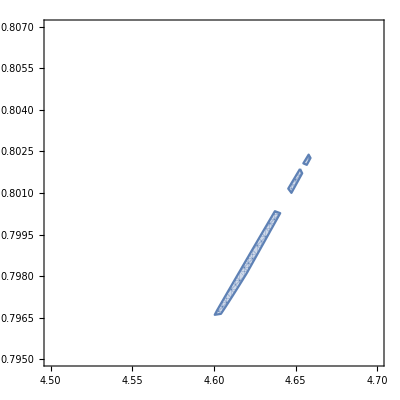

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[10] /. g -> 1], # ≥ 0 &], {E0, 4.50, 4.70}, {x2, 0.795, 0.807}]
```

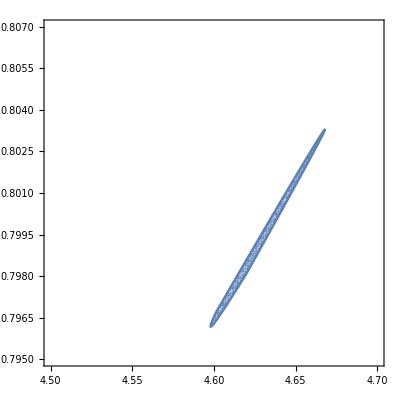

```mathematica
RegionPlot[AllTrue[Eigenvalues[matPositive[10] /. g -> 1], # ≥ 0 &], {E0, 4.50, 4.70}, {x2, 0.795, 0.807}, PlotPoints->100]
```

```mathematica
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[7] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}][[1]]
```

1.3609

```mathematica
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[8] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}][[1]]
```

1.36362

```mathematica
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[9] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}][[1]]
```

1.3865

```mathematica
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[10] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}]
```

{1.3865,{x2→0.304344,E0→1.3865}}

```mathematica
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[11] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}]
```

{1.3922,{x2→0.305782,E0→1.3922}}

```mathematica
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[12] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}]
```

{1.3922,{x2→0.305781,E0→1.3922}}

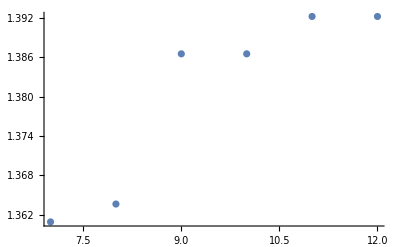

```mathematica
ListPlot[{{7, 1.360900449104947}, {8, 1.363621606322767}, {9, 1.3865039748817591}, {10, 1.3865039748792434}, {11, 1.3921989769203813}, {12, 1.3921989772554817}}]
```